Which characters should appear in the pullback?
Before we take the pullback it would be nice to reduce the characters that would appear in the Coset CFT character expansion in TIsing^2 characters.

```mathematica
p=5;
p'=4;
cv=1-6(p-p')^2/(p p')//Echo[#,"c = "]&;
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
hvf[i_,j_]:=hv@@i+hv@@j;
H={{1,1},{1,2},{1,3},{1,4},{2,2},{2,4}};

Hf=Tuples[H,2];
ηinv[q_,N_:∞]:=∑_(k=0)^N PartitionsP[k] q^k;
χv[r_,s_,q_,N_:∞,e_:1,f_:1]:=Series[ηinv[f q^e](f q^e)^(-1/24-(r s)/2+(p r^2)/(4 p')+(s^2 p')/(4 p))∑_(n=-N)^N ((f q^e)^(n^2 p p'+n (p r-s p'))-(f q^e)^(n^2 p p'+n (p r+s p')+r s)),{q,0,N}];
χvI[r_,s_,q_,N_:∞,e_:1,f_:1]:=Series[ηinv[f q^e]∑_(n=-N)^N ((f q^e)^(n^2 p p'+n (p r-s p'))-(f q^e)^(n^2 p p'+n (p r+s p')+r s)),{q,0,N}];
χvf[i_,j_,q_,N_]:=χv[i[[1]],i[[2]],q,N]χv[j[[1]],j[[2]],q,N];
```

c =   7/10

```mathematica
r=1; s=3;
n=10;
hv[r,s]
```

3/5

```mathematica
Assuming[q>0,Simplify[1/2 q^(-((3cv)/48+1/2 hv[r,s])+cv/12)(χv[r,s,q,n,1/2]+ⅇ^(-π ⅈ (hv[r,s]-cv/24)) χv[r,s,q,n,1/2,-1])]]
```

1+2 q+4 q^2+7 q^3+13 q^4+22 q^5+36 q^6+58 q^7+91 q^8+139 q^9+O[q]^10

```mathematica
Assuming[q>0,Simplify[1/2 q^(-((3cv)/48+1/2+1/2 hv[r,s])+cv/12)(χv[r,s,q,n,1/2]-ⅇ^(-π ⅈ (hv[r,s]-cv/24)) χv[r,s,q,n,1/2,-1])]]
```

1+2 q+5 q^2+9 q^3+16 q^4+27 q^5+45 q^6+71 q^7+111 q^8+169 q^9+O[q]^(19/2)

```mathematica
k=8;
cw=(2(k-1))/(k+2);
hw[l_,m_]:=(l(l+2))/(4(k+2))-m^2/(4k);
χw[l_,m_,q_,N_:∞]:=Series[ηinv[q]^2∑_(r=0)^N ∑_(s=0)^N (-1)^(r+s)(q^(1/2 (r^2+s (1+l-m+s)+r (1+l+m+18 s)))-q^(1/2 (18+r^2+s (19+m+s)-l (2+r+s)+r (19-m+18 s)))),{q,0,N}];
χM[A_,q_,χ_,N_:∞]:=χ[A[[1,1]],A[[1,2]],q,N]χ[A[[2,1]],A[[2,2]],q,N];
(*This is the super ugly way to calculate which are the possible values l,m without degeneracies*)
w=ConstantArray[0,{k+1,2k+1}];
M[m_]:=m+k+1;
L[l_]:=l+1
For[l=0,l<=k,l++,For[m=-l,m<=l,m=m+2,If[w[[L[l],M[m]]]==0,w[[L[l],M[m]]]=1;If[0<M[k-m]<=2k+1,w[[L[k-l],M[k-m]]]=-1];If[0<M[k+m]<=2k+1,w[[L[k-l],M[k+m]]]=-1];]]]
W={#[[1]]-1,#[[2]]-k-1}&/@Position[w,_?(# ==1&),{2}];
```

The conformal weights of the two models

TIsing^2

```mathematica
Sort[hvf @@@Hf]
```

{0,3/80,3/80,3/40,1/10,1/10,11/80,11/80,1/5,7/16,7/16,19/40,19/40,43/80,43/80,3/5,3/5,51/80,51/80,7/10,7/10,7/8,83/80,83/80,6/5,3/2,3/2,123/80,123/80,8/5,8/5,31/16,31/16,21/10,21/10,3}

Coset

```mathematica
Sort[hw @@@W]
```

{0,7/160,7/160,3/40,3/40,3/32,3/32,1/10,1/5,11/32,11/32,19/40,19/40,19/32,19/32,3/5,7/10,7/10,127/160,127/160,27/32,27/32,7/8,7/8,43/40,43/40,6/5,207/160,207/160,3/2,3/2,247/160,247/160,15/8,15/8,2}

Now let’s find the compatible combinations of characters

```mathematica
nonNegInt[x_]:=IntegerQ[x]&&x>=0
Wpairs=Tuples[W,2];
Hfpairs=Tuples[Hf,2];
weightsM=Sort[DeleteDuplicates[(hw@@#1+hw@@#2)&@@@Wpairs]];
allowedModules=Function[h,{h,Hfpairs[[Position[Hfpairs,_?(nonNegInt[(hvf@@#1+hvf@@#2)&@@# - h]&),1]//Flatten]]}]/@weightsM;
weightsToModules=Function[h,{h,Wpairs[[Position[Wpairs,_?((hw@@#1+hw@@#2)&@@# == h&),1]//Flatten]]}]/@weightsM;
```

```mathematica
n=10;
i=62;
h=allowedModules[[i,1]];
min= Min[(hvf@@#1+hvf@@#2)&@@#-h &/@allowedModules[[i,2]]];
cpf=DeleteDuplicates[q^(-Min[min,0])χM[#,q,χw,n]&/@weightsToModules[[i,2]]][[1]];
pfs= DeleteDuplicates[q^((hvf@@#1+hvf@@#2)&@@#-h+Min[min,0])χM[#,q,χvf,n]&/@allowedModules[[i,2]]];
Coefficients[allowedModules_,weightsToModules_,n_:10]:=(
h=allowedModules[[1]];
min= Min[(hvf@@#1+hvf@@#2)&@@#-h &/@allowedModules[[2]]];
targetPf=DeleteDuplicates[q^Min[min,0] χM[#,q,χw,n]&/@weightsToModules[[2]]][[1]];
pfs= DeleteDuplicates[q^((hvf@@#1+hvf@@#2)&@@#-h-Min[min,0])χM[#,q,χvf,n]&/@allowedModules[[2]]];
If[pfs=={},{},Quiet@Check[LinearSolve[Transpose[CoefficientList[#,q,n]&@pfs],CoefficientList[targetPf,q,n]],{},LinearSolve::nosol]]);
PullbackMatrix=MapThread[{#1[[1]],Coefficients[#1,#2,20]}&,{allowedModules,weightsToModules}];
```

```mathematica
Length[PullbackMatrix]-Length[Position[Transpose[PullbackMatrix][[2]],_?(#=={}&),1]]
PullbackMatrix//MatrixForm
```

0

(0 | {}
7/160 | {}
3/40 | {}
7/80 | {}
3/32 | {}
1/10 | {}
19/160 | {}
11/80 | {}
23/160 | {}
3/20 | {}
27/160 | {}
7/40 | {}
3/16 | {}
31/160 | {}
1/5 | {}
39/160 | {}
11/40 | {}
47/160 | {}
3/10 | {}
11/32 | {}
31/80 | {}
2/5 | {}
67/160 | {}
7/16 | {}
71/160 | {}
19/40 | {}
83/160 | {}
87/160 | {}
11/20 | {}
91/160 | {}
23/40 | {}
19/32 | {}
3/5 | {}
51/80 | {}
103/160 | {}
107/160 | {}
27/40 | {}
11/16 | {}
111/160 | {}
7/10 | {}
119/160 | {}
31/40 | {}
127/160 | {}
4/5 | {}
131/160 | {}
67/80 | {}
27/32 | {}
139/160 | {}
7/8 | {}
71/80 | {}
143/160 | {}
9/10 | {}
147/160 | {}
15/16 | {}
151/160 | {}
19/20 | {}
31/32 | {}
39/40 | {}
159/160 | {}
167/160 | {}
171/160 | {}
43/40 | {}
179/160 | {}
91/80 | {}
23/20 | {}
187/160 | {}
47/40 | {}
19/16 | {}
191/160 | {}
6/5 | {}
39/32 | {}
199/160 | {}
203/160 | {}
51/40 | {}
207/160 | {}
13/10 | {}
211/160 | {}
107/80 | {}
27/20 | {}
219/160 | {}
111/80 | {}
223/160 | {}
7/5 | {}
227/160 | {}
23/16 | {}
231/160 | {}
47/32 | {}
59/40 | {}
239/160 | {}
3/2 | {}
247/160 | {}
31/20 | {}
63/40 | {}
127/80 | {}
51/32 | {}
8/5 | {}
259/160 | {}
131/80 | {}
263/160 | {}
267/160 | {}
67/40 | {}
27/16 | {}
17/10 | {}
55/32 | {}
279/160 | {}
7/4 | {}
283/160 | {}
71/40 | {}
287/160 | {}
9/5 | {}
59/32 | {}
299/160 | {}
15/8 | {}
151/80 | {}
303/160 | {}
19/10 | {}
307/160 | {}
39/20 | {}
63/32 | {}
79/40 | {}
319/160 | {}
2 | {}
323/160 | {}
327/160 | {}
83/40 | {}
167/80 | {}
67/32 | {}
21/10 | {}
171/80 | {}
343/160 | {}
43/20 | {}
347/160 | {}
11/5 | {}
71/32 | {}
359/160 | {}
91/40 | {}
367/160 | {}
187/80 | {}
75/32 | {}
47/20 | {}
379/160 | {}
19/8 | {}
191/80 | {}
12/5 | {}
387/160 | {}
79/32 | {}
99/40 | {}
399/160 | {}
103/40 | {}
207/80 | {}
83/32 | {}
13/5 | {}
419/160 | {}
427/160 | {}
27/10 | {}
87/32 | {}
439/160 | {}
11/4 | {}
447/160 | {}
227/80 | {}
91/32 | {}
23/8 | {}
59/20 | {}
3 | {}
487/160 | {}
123/40 | {}
247/80 | {}
507/160 | {}
16/5 | {}
527/160 | {}
27/8 | {}
547/160 | {}
7/2 | {}
567/160 | {}
15/4 | {}
31/8 | {}
4 | {})

```mathematica
weightsC=Sort[DeleteDuplicates[hw@@@W]];
allowedCharacters=Function[h,{h,Hf[[Position[Hf,_?((hvf@@# - h)∈Integers&),1]//Flatten]]}]/@weightsC;
weightsToCharacters=Function[h,{h,W[[Position[W,_?(hw@@# == h&),1]//Flatten]]}]/@weightsC;
```

```mathematica
n=10;
i=5;
h=allowedCharacters[[i,1]];
cpf=DeleteDuplicates[χw[#[[1]],#[[2]],q,n]&/@weightsToCharacters[[i,2]]][[1]];
pfs= DeleteDuplicates[q^((hvf@@#)&@#-h)χvf[#[[1]],#[[2]],q,n]&/@allowedCharacters[[i,2]]];
x=LinearSolve[Transpose[CoefficientList[#,q,n]&@pfs],CoefficientList[cpf,q,n]]
Total[x*pfs]-cpf
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{q^(1/24)+q^(25/24)+2 q^(49/24)+4 q^(73/24)+7 q^(97/24)+11 q^(121/24)+19 q^(145/24)+29 q^(169/24)+46 q^(193/24)+69 q^(217/24),q^(97/24)+2 q^(121/24)+5 q^(145/24)+8 q^(169/24)+15 q^(193/24)+24 q^(217/24)+40 q^(241/24)+61 q^(265/24)+95 q^(289/24)},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{1,1,3,6,12,19,34,53,86,130}]

LinearSolve::nosol: Linear equation encountered that has no solution.

$Aborted

The Modular S matrix of the Coset Model
In our effort to find the Cardy states in the gauged theory we want to calculate the S matrix and express the Cardy states as linear combinations of the Ishibashi states in the coset model using coefficients from the S-matrix. The matrix is given by

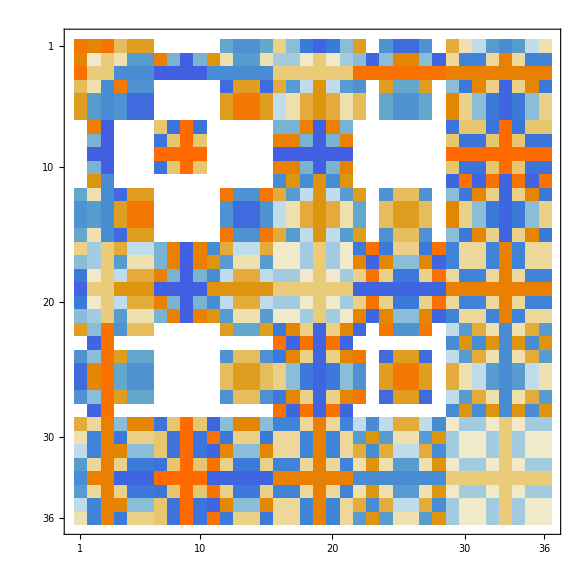

```mathematica
S=Array[(1/(√(2(k+2)))Sin[(π(W[[#1,1]]+1)(W[[#2,1]]+1))/(k+2)] ⅇ^(-ⅈ π (W[[#1,2]]W[[#2,2]])/(k+2)))&,{Length[W],Length[W]}]//Simplify;
S//MatrixPlot
```